## Eigenvalues

```mathematica
lines1S1SL0=<|"4"->Import["lines/line_1S1S_L0_dim4.mx"],"10"->Import["lines/line_1S1S_L0_dim10.mx"],"20"->Import["lines/line_1S1S_L0_dim20.mx"],"horizontalLine"->Table[{omega,3.67423},{omega,0.5,2.5,0.5}]|>;
```

```mathematica
color1=Black;
color2=RGBColor[0.09,0.82,0.88];
color3=Black;
p1=ListPlot[{lines1S1SL0["4"],lines1S1SL0["10"],lines1S1SL0["20"],lines1S1SL0["horizontalLine"]},
Joined->True,PlotStyle->{{color1,Dashing[{0.03,0.018,0.006,0.018}],Thickness[0.011]},{color2,Thickness[0.011]},{color3,Thickness[0.011]},{Black,Dashed,Thickness[0.007]}},LabelStyle->{FontSize->18,FontFamily->"Times",Black},Frame->{{True,True},{True,True}},
GridLines->Automatic,
FrameLabel->{{"E",None},{"ω",None}},
PlotLabel->"1S1S",
PlotLegends->Placed[{"N_Q=4","N_Q=10","N_Q=20","E_analytical"},{Center,Top}],PlotRange->{{0.47,2.53},{3.67,3.83}},
Prolog->{Lighter[Lighter[LightGray]], Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},
AspectRatio->1.3
]
```

-Graphics-

```mathematica
lines1S2SL0=<|"4"->Import["lines/line_1S2S_L0_dim4.mx"],"10"->Import["lines/line_1S2S_L0_dim10.mx"],"20"->Import["lines/line_1S2S_L0_dim20.mx"],"horizontalLine"->Table[{omega,6.12372},{omega,0.5,2.5,0.5}]|>;
```

```mathematica
color1=Black;
color2=RGBColor[0.09,0.82,0.88];
color3=Black;
p2=ListPlot[{lines1S2SL0["4"],lines1S2SL0["10"],lines1S2SL0["20"],lines1S2SL0["horizontalLine"]},
AspectRatio->1.3,
Joined->True,PlotStyle->{{color1,Dashing[{0.03,0.018,0.006,0.018}],Thickness[0.011]},{color2,Thickness[0.011]},{color3,Thickness[0.011]},{Black,Dashed,Thickness[0.007]}},LabelStyle->{FontSize->18,FontFamily->"Times",Black},Frame->{{True,True},{True,True}},
GridLines->Automatic,
FrameLabel->{{"E",None},{"ω",None}},
PlotLabel->"1S2S",
PlotLegends->Placed[{"N_Q=4","N_Q=10","N_Q=20","E_analytical"},{Center,Top}],PlotRange->{{0.47,2.53},{6.07,8.3}},
Prolog->{Lighter[Lighter[LightGray]], Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}
]
```

-Graphics-

```mathematica
lines1D1DL0=<|"4"->Import["lines/line_1D1D_L0_dim10.mx"],"10"->Import["lines/line_1D1D_L0_dim20.mx"],"20"->Import["lines/line_1D1D_L0_dim35.mx"],"horizontalLine"->Table[{omega,8.57321},{omega,0.5,2.5,0.5}]|>;
```

```mathematica
color1=Black;
color2=RGBColor[0.09,0.82,0.88];
color3=Black;
p3=ListPlot[{lines1D1DL0["4"],lines1D1DL0["10"],lines1D1DL0["20"],lines1D1DL0["horizontalLine"]},
AspectRatio->1.3,
Joined->True,PlotStyle->{{color1,Dashing[{0.03,0.018,0.006,0.018}],Thickness[0.011]},{color2,Thickness[0.011]},{color3,Thickness[0.011]},{Black,Dashed,Thickness[0.007]}},LabelStyle->{FontSize->18,FontFamily->"Times",Black},Frame->{{True,True},{True,True}},
GridLines->Automatic,
FrameLabel->{{"E",None},{"ω",None}},
PlotLabel->"1D1D",
PlotLegends->Placed[{"N_Q=10","N_Q=20","N_Q=35","E_analytical"},{Center,Top}],PlotRange->{{0.47,2.53},{8.5,11.5}},
Prolog->{Lighter[Lighter[LightGray]], Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}
]
```

-Graphics-

```mathematica
Export["plots/eigenvalues/equalM_1D1D_L0.pdf",p3,"PDF","AllowRasterization"->False]
```

plots/eigenvalues/equalM_1D1D_L0.pdf

## Eigenvectors

```mathematica
vectors=<|"1"->Import["lines/vector_components/equalM_1S1S_dim4.mx"],
"2"->Import["lines/vector_components/equalM_1S1S_dim10.mx"],
"3"->Import["lines/vector_components/equalM_1S1S_dim20.mx"],
"horizontal"->Table[{omega,1},{omega,0.5,2.5,0.5}]|>;
```

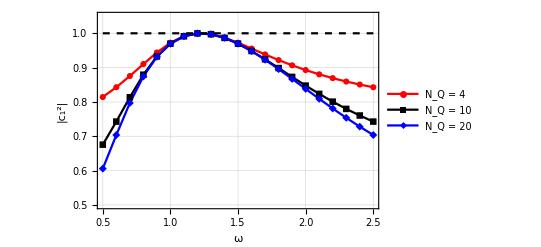

```mathematica
xaxis10S={"1S1S","1S2S","1P1P","2S1S","1S3S","1P2P","1D1D","2S2S","2P1P","3S1S"};
eigenvectorPlot=ListPlot[
{vectors["1"],vectors["2"],vectors["3"],vectors["horizontal"]},
Joined->True,
(*FrameTicks->{{Automatic,None}, {Transpose[{Range[10],xaxis10S}],None}},*)
FrameTicks->{{Automatic,None}, {Automatic,None}},
AxesOrigin->{0.5,0},
LabelStyle->{FontSize->12, FontFamily->"Times",Black},
Frame->{{True,True},{True,True}},
(*PlotRange->{{0.7,10.2},{0,1}},*)
PlotRange->{0.5,1.05},
PlotStyle->{Red,Black,Blue,{Black,Dashed}},
FrameStyle->Thickness->0.0055,
(*Filling->Axis,*)
PlotLegends->Placed[{Style["N_Q = 4",FontSize->14,FontFamily->"Times"],Style["N_Q = 10",FontSize->14,FontFamily->"Times"],
Style["N_Q = 20",FontSize->14,FontFamily->"Times"]},{Center,Bottom}],
GridLines->Automatic,
GridLinesStyle->Directive[Gray,Dashed,Thickness->0.0005],
FrameLabel->{{"|c_1^2|",None},{"ω",None}},
PlotMarkers->{Automatic,Automatic,Automatic,None}
]
```

```mathematica
Export["plots/vector_components/equalM_1S1S.pdf",eigenvectorPlot,"PDF","AllowRasterization"->False]
```

plots/vector_components/equalM_1S1S.pdf

## Expectation Values

```mathematica
expValues=<|"0"->Import["lines/expValues/equalM_delta32_1S1S_dim4.mx"],"1"->Import["lines/expValues/equalM_delta32_1S1S_dim10.mx"],
"2"->Import["lines/expValues/equalM_delta32_1S1S_dim20.mx"],
"horizontal"->Table[{omega,0.0860595},{omega,0.5,2.5,0.1}],
"vertical"->Table[{√(3/2),y},{y,0.085,0.087,0.0001}]|>;
```

```mathematica
expValues["2"]
```

{{0.5,1.66481},{0.6,1.59986},{0.7,1.57439},{0.8,1.56688},{0.9,1.5653},{1.,1.5651},{1.1,1.56508},{1.2,1.56508},{1.3,1.56508},{1.4,1.56508},{1.5,1.56507},{1.6,1.56501},{1.7,1.56478},{1.8,1.56423},{1.9,1.56316},{2.,1.56134}}

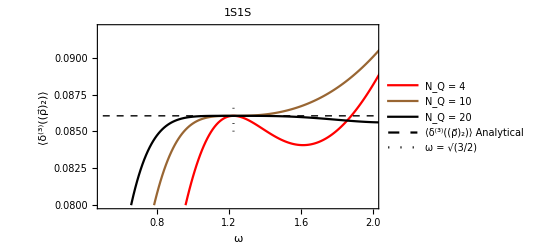

```mathematica
expValuePlot=ListPlot[{expValues["0"],expValues["1"],expValues["2"],expValues["horizontal"],expValues["vertical"]},
Joined->True,
Frame->{{True,True},{True,True}},
FrameStyle->Thickness->0.0055,
FrameLabel->{{"⟨δ^(3)((ρ⃗)_2)⟩",None},{"ω",None}},
FrameTicks->{{Automatic,None}, {Automatic,None}},
LabelStyle->{FontSize->14, FontFamily->"Times",Black},
(*Filling->2.44949,*)
PlotRange->{{0.5,2},{0.080,0.092}},
PlotLegends->{Placed[{Style["N_Q = 4",FontSize->13,FontFamily->"Times"],Style["N_Q = 10",FontSize->13,FontFamily->"Times"],
Style["N_Q = 20",FontSize->13,FontFamily->"Times"]},{Left,Top}],
Placed[{None,None,None,Style["⟨δ^(3)((ρ⃗)_2)⟩ Analytical",FontSize->13,FontFamily->"Times"],Style["ω = √(3/2)",FontSize->13,FontFamily->"Times"]},{Right,Bottom}]},
PlotStyle->{{Red},{Brown},{Black},{Black,Dashed,Thin},{Black,Dotted}},
PlotLabel->"1S1S"
]
```

```mathematica
Export["plots/expValues/equalM_delta32_1S1S.pdf",expValuePlot,"PDF","AllowRasterization"->False]
```

plots/expValues/equalM_delta32_1S1S.pdf

## Component of Eigenvector

```mathematica
ListPlot[{line1,line2,line3,line4,horizontal},Joined->True,PlotMarkers->Automatic,
PlotRange->{0.4,1.02}]
```